{3275,3415,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,39894,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,3310}
 |  |  |  |

```mathematica
particleDistribution=Import["C:\\Users\\leon_\\SERD model Python code\\NewTextFile.txt"];
particleDistribution1=ToExpression["{"<>StringDrop[StringDrop[particleDistribution,1],-1]<>"}"];
sampleSize=ToExpression[Import["C:\\Users\\leon_\\SERD model Python code\\sampleSize.txt"]];
```

```mathematica
particleDistribution1
```

{3288,3340,3372,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,39894,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}
 |  |  |  |

```mathematica
systEv=Partition[particleDistribution1,200];
```

{1}
 |  |  |  |

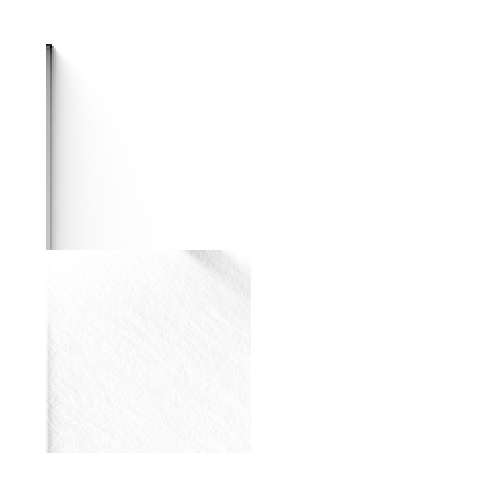

{{0.335637,0.175716,0.192498,0.168806,0.189536,0.151037,0.144126,0.12537,184,0.,0.,0.,0.,0.,0.,0.,0.},198,{1}}
 |  |  |  |

```mathematica
systEv=Partition[particleDistribution1,200]
systEv2=Table[N[If[sampleSize[[i1]]>0,systEv[[i1]]/sampleSize[[i1]],Table[0,{i2,200}]]],{i1,200}];
ArrayPlot[systEv2]
```

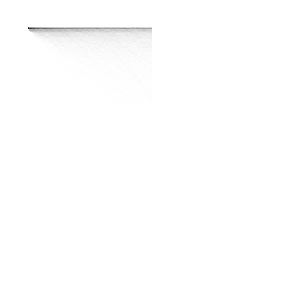

```mathematica
ArrayPlot[systEv2]
```

{1}
 |  |  |  |

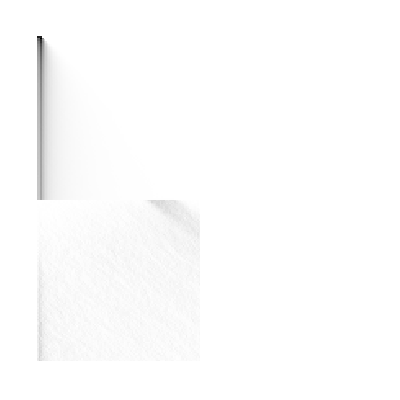

```mathematica
particleDistribution=Import["C:\\Users\\leon_\\SERD model Python code\\NewTextFile.txt"];
particleDistribution1=ToExpression["{"<>StringDrop[StringDrop[particleDistribution,1],-1]<>"}"];
sampleSize=ToExpression[Import["C:\\Users\\leon_\\SERD model Python code\\sampleSize.txt"]];
systEv=Partition[particleDistribution1,200]
systEv2=Table[N[If[sampleSize[[i1]]>0,systEv[[i1]]/sampleSize[[i1]],Table[0,{i2,200}]]],{i1,200}];
ArrayPlot[systEv2]
```

{1}
 |  |  |  |

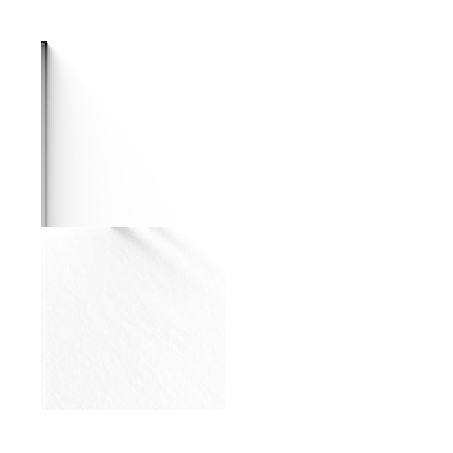

```mathematica
particleDistribution=Import["C:\\Users\\leon_\\SERD model Python code\\NewTextFile.txt"];
particleDistribution1=ToExpression["{"<>StringDrop[StringDrop[particleDistribution,1],-1]<>"}"];
sampleSize=ToExpression[Import["C:\\Users\\leon_\\SERD model Python code\\sampleSize.txt"]];
systEv=Partition[particleDistribution1,200]
systEv2=Table[N[If[sampleSize[[i1]]>0,systEv[[i1]]/sampleSize[[i1]],Table[0,{i2,200}]]],{i1,200}];
ArrayPlot[systEv2]
```

{1}
 |  |  |  |

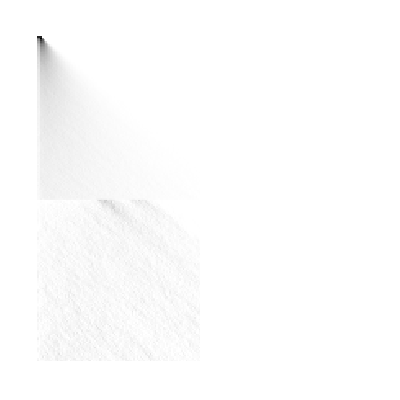

```mathematica
particleDistribution=Import["C:\\Users\\leon_\\SERD model Python code\\NewTextFile.txt"];
particleDistribution1=ToExpression["{"<>StringDrop[StringDrop[particleDistribution,1],-1]<>"}"];
sampleSize=ToExpression[Import["C:\\Users\\leon_\\SERD model Python code\\sampleSize.txt"]];
systEv=Partition[particleDistribution1,200]
systEv2=Table[N[If[sampleSize[[i1]]>0,systEv[[i1]]/sampleSize[[i1]],Table[0,{i2,200}]]],{i1,200}];
ArrayPlot[systEv2]
```

{1}
 |  |  |  |

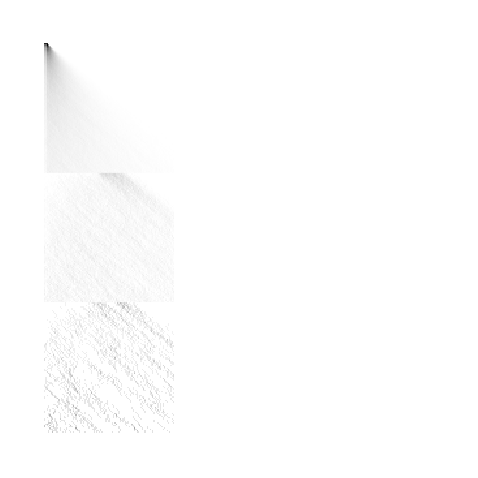

```mathematica
particleDistribution=Import["C:\\Users\\leon_\\SERD model Python code\\NewTextFile.txt"];
particleDistribution1=ToExpression["{"<>StringDrop[StringDrop[particleDistribution,1],-1]<>"}"];
sampleSize=ToExpression[Import["C:\\Users\\leon_\\SERD model Python code\\sampleSize.txt"]];
systEv=Partition[particleDistribution1,300]
systEv2=Table[N[If[sampleSize[[i1]]>0,systEv[[i1]]/sampleSize[[i1]],Table[0,{i2,300}]]],{i1,300}];
ArrayPlot[systEv2]
```

{1}
 |  |  |  |

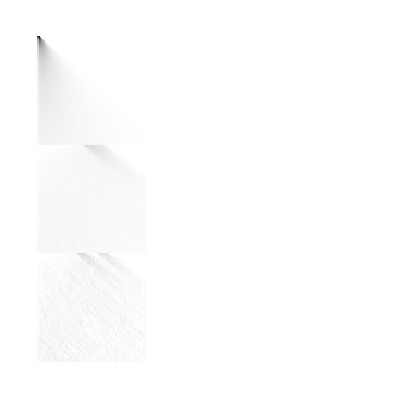

```mathematica
particleDistribution=Import["C:\\Users\\leon_\\SERD model Python code\\NewTextFile.txt"];
particleDistribution1=ToExpression["{"<>StringDrop[StringDrop[particleDistribution,1],-1]<>"}"];
sampleSize=ToExpression[Import["C:\\Users\\leon_\\SERD model Python code\\sampleSize.txt"]];
systEv=Partition[particleDistribution1,300]
systEv2=Table[N[If[sampleSize[[i1]]>0,systEv[[i1]]/sampleSize[[i1]],Table[0,{i2,300}]]],{i1,300}];
ArrayPlot[systEv2]
```

{1}
 |  |  |  |

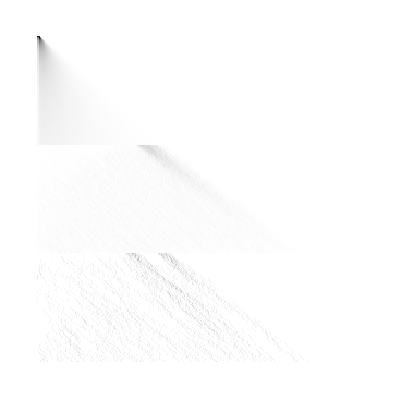

```mathematica
particleDistribution=Import["C:\\Users\\leon_\\SERD model Python code\\NewTextFile.txt"];
particleDistribution1=ToExpression["{"<>StringDrop[StringDrop[particleDistribution,1],-1]<>"}"];
sampleSize=ToExpression[Import["C:\\Users\\leon_\\SERD model Python code\\sampleSize.txt"]];
systEv=Partition[particleDistribution1,300]
systEv2=Table[N[If[sampleSize[[i1]]>0,systEv[[i1]]/sampleSize[[i1]],Table[0,{i2,300}]]],{i1,300}];
ArrayPlot[systEv2]
```

{1}
 |  |  |  |

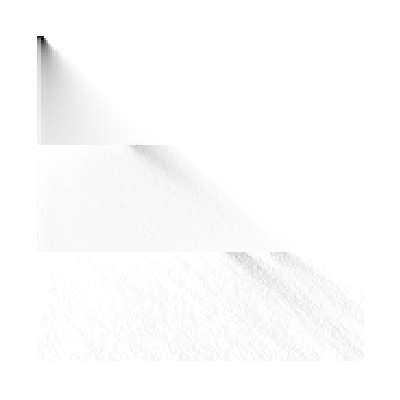

```mathematica
particleDistribution=Import["C:\\Users\\leon_\\SERD model Python code\\NewTextFile.txt"];
particleDistribution1=ToExpression["{"<>StringDrop[StringDrop[particleDistribution,1],-1]<>"}"];
sampleSize=ToExpression[Import["C:\\Users\\leon_\\SERD model Python code\\sampleSize.txt"]];
systEv=Partition[particleDistribution1,150]
systEv2=Table[N[If[sampleSize[[i1]]>0,systEv[[i1]]/sampleSize[[i1]],Table[0,{i2,150}]]],{i1,150}];
ArrayPlot[systEv2]
```

{1}
 |  |  |  |

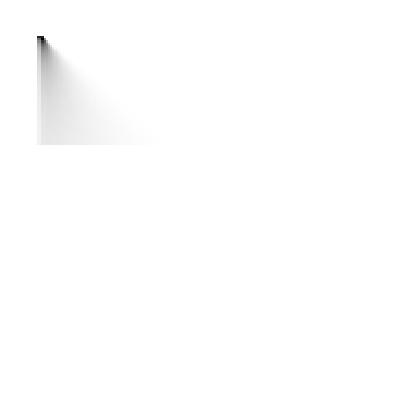

```mathematica
particleDistribution=Import["C:\\Users\\leon_\\SERD model Python code\\NewTextFile.txt"];
particleDistribution1=ToExpression["{"<>StringDrop[StringDrop[particleDistribution,1],-1]<>"}"];
sampleSize=ToExpression[Import["C:\\Users\\leon_\\SERD model Python code\\sampleSize.txt"]];
systEv=Partition[particleDistribution1,150]
systEv2=Table[N[If[sampleSize[[i1]]>0,systEv[[i1]]/sampleSize[[i1]],Table[0,{i2,150}]]],{i1,150}];
ArrayPlot[systEv2]
```

{1}
 |  |  |  |

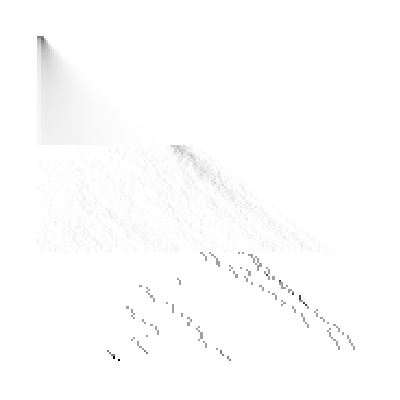

```mathematica
particleDistribution=Import["C:\\Users\\leon_\\SERD model Python code\\NewTextFile.txt"];
particleDistribution1=ToExpression["{"<>StringDrop[StringDrop[particleDistribution,1],-1]<>"}"];
sampleSize=ToExpression[Import["C:\\Users\\leon_\\SERD model Python code\\sampleSize.txt"]];
systEv=Partition[particleDistribution1,150]
systEv2=Table[N[If[sampleSize[[i1]]>0,systEv[[i1]]/sampleSize[[i1]],Table[0,{i2,150}]]],{i1,150}];
ArrayPlot[systEv2]
```

{1}
 |  |  |  |

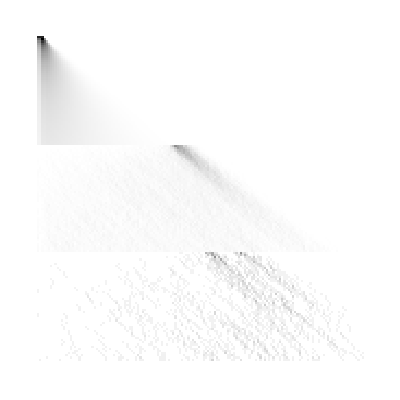

```mathematica
particleDistribution=Import["C:\\Users\\leon_\\SERD model Python code\\NewTextFile.txt"];
particleDistribution1=ToExpression["{"<>StringDrop[StringDrop[particleDistribution,1],-1]<>"}"];
sampleSize=ToExpression[Import["C:\\Users\\leon_\\SERD model Python code\\sampleSize.txt"]];
systEv=Partition[particleDistribution1,150]
systEv2=Table[N[If[sampleSize[[i1]]>0,systEv[[i1]]/sampleSize[[i1]],Table[0,{i2,150}]]],{i1,150}];
ArrayPlot[systEv2]
```

```mathematica
particleDistribution=Import["C:\\Users\\leon_\\SERD model Python code\\NewTextFile.txt"];
particleDistribution1=ToExpression["{"<>StringDrop[StringDrop[particleDistribution,1],-1]<>"}"];
sampleSize=ToExpression[Import["C:\\Users\\leon_\\SERD model Python code\\sampleSize.txt"]];
systEv=Partition[particleDistribution1,1000]
systEv2=Table[N[If[sampleSize[[i1]]>0,systEv[[i1]]/sampleSize[[i1]],Table[0,{i2,1000}]]],{i1,1000}];
ArrayPlot[systEv2]
```

{1}
 |  |  |  |

-Graphics-

```mathematica
particleDistribution=Import["C:\\Users\\leon_\\SERD model Python code\\NewTextFile.txt"];
particleDistribution1=ToExpression["{"<>StringDrop[StringDrop[particleDistribution,1],-1]<>"}"];
sampleSize=ToExpression[Import["C:\\Users\\leon_\\SERD model Python code\\sampleSize.txt"]];
systEv=Partition[particleDistribution1,1000]
systEv2=Table[N[If[sampleSize[[i1]]>0,systEv[[i1]]/sampleSize[[i1]],Table[0,{i2,1000}]]],{i1,1000}];
ArrayPlot[systEv2]
```

{1}
 |  |  |  |

-Graphics-